# Create Data

## Program

### R <-> MMA

```mathematica
makeClusterFromRdata[rdata_]:=Map[Drop[#,-1]&,Gather[Map[Drop[#,1]&,Drop[rdata,1]],#1[[-1]]==#2[[-1]]&],{2}]
```

```mathematica
makeClusterFromRdata[rdata_,"Nohead"]:=Map[Drop[#,-1]&,Gather[Map[Drop[#,1]&,rdata],#1[[-1]]==#2[[-1]]&],{2}]
```

```mathematica
makeClusterFromRdata[rdata_,"NoID"]:=Map[Drop[#,-1]&,Gather[Drop[rdata,1],#1[[-1]]==#2[[-1]]&],{2}]
```

```mathematica
makeClusterFromRdata[rdata_,op__]:=If[
Length[Flatten[Union[{{op},{"NoID","Nohead"}}]]]==2,
Map[Drop[#,-1]&,Gather[rdata,#1[[-1]]==#2[[-1]]&],{2}]
]
```

```mathematica
(*makeClusterFromRdata[rdata_,"NoID","Nohead"]:=Map[Drop[#,-1]&,Gather[rdata,#1[[-1]]==#2[[-1]]&],{2}]*)
```

```mathematica
makeRClusterFromMMAClData[cl_List]:=Module[
{len,dim,ClIDs},
len=Length[cl];
dim=Length[cl[[1,1]]];
ClIDs=Table[i,{i,len}];
Flatten[Table[Map[Append[#,i]&,cl[[i]]],{i,len}],1]
]
```

```mathematica
reginMax=1
```

1

```mathematica
regionMin=-1
```

-1

```mathematica
Get["/Users/amanokou/SCRIPT-MATHEMATICA/SCRIPTS/polar.txt"]
```

```mathematica
SetDirectory["/Users/amanokou/gitsrc/ClusteringAdequation/data"]
```

/Users/amanokou/gitsrc/ClusteringAdequation/data

```mathematica
createClusterdFileR[li_]:=Flatten[Table[Map[Append[#,n]&,li[[n]]],{n,Length[li]}],1]
```

```mathematica
testli2D={{{1,2},{1,2},{3,2}},{{3,3},{4,3}},{{4,4},{5,1},{1,4}},{{2,6},{4,6},{6,6},{7,1}}}
```

{{{1,2},{1,2},{3,2}},{{3,3},{4,3}},{{4,4},{5,1},{1,4}},{{2,6},{4,6},{6,6},{7,1}}}

```mathematica
createClusterdFileR[testli2D]
```

{{1,2,1},{1,2,1},{3,2,1},{3,3,2},{4,3,2},{4,4,3},{5,1,3},{1,4,3},{2,6,4},{4,6,4},{6,6,4},{7,1,4}}

## 2D, background, 200 - 1000; 200

```mathematica
bg[2][200]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{200}];
```

```mathematica
bg[2][400]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{400}];
```

```mathematica
bg[2][600]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{600}];
```

```mathematica
bg[2][800]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{800}];
```

```mathematica
bg[2][1000]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{1000}];
```

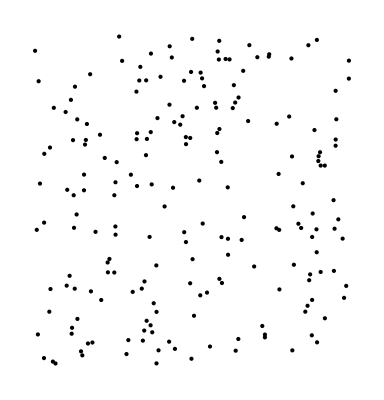

```mathematica
Graphics[Map[Point[#]&,bg[2][200]]]
```

```mathematica
(*Export["bg-2-200.tsv",bg[2][200]]*)
```

```mathematica
(*Export["bg-2-400.tsv",bg[2][400]]*)
```

```mathematica
(*Export["bg-2-600.tsv",bg[2][600]]*)
```

```mathematica
(*Export["bg-2-800.tsv",bg[2][800]]*)
```

```mathematica
(*Export["bg-2-1000.tsv",bg[2][1000]]*)
```

## 2D, normaldist;single, 2 - 20; 2

```mathematica
nd[2][2]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{2}];
```

```mathematica
For[i=2,i≤20,i+=2,Print[i];
nd[2][i]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{i}];
]
```

2

4

6

8

10

12

14

16

18

20

## 2D, normaldist;single, 200 - 1600; 200

```mathematica
nd[2][200]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{200}];
```

```mathematica
nd[2][400]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{400}];
```

```mathematica
nd2[2][400]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{400}];
```

```mathematica
nd[2][600]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{600}];
```

```mathematica
nd[2][800]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{800}];
```

```mathematica
nd[2][1000]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{1000}];
```

```mathematica
nd[2][1200]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{1200}];
```

```mathematica
nd[2][1400]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{1400}];
```

```mathematica
nd[2][1600]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{1600}];
```

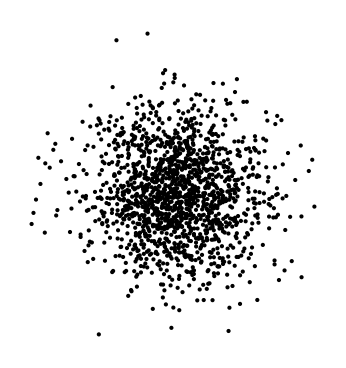

```mathematica
Graphics[Map[Point[#]&,nd[2][1600]]]
```

## 2D, 3Cls

```mathematica
correctdata[2][2][3]={Map[#+{0,0}&,nd[2][2]],Map[#+{5,0}&,nd[2][2]],Map[#+{2.5,3.5}&,nd[2][2]]}
```

{{{-0.688014,-0.0668755},{0.63496,-0.73258}},{{4.31199,-0.0668755},{5.63496,-0.73258}},{{1.81199,3.43312},{3.13496,2.76742}}}

```mathematica
makeRClusterFromMMAClData[correctdata[2][2][3]]
```

{{-0.688014,-0.0668755,1},{0.63496,-0.73258,1},{4.31199,-0.0668755,2},{5.63496,-0.73258,2},{1.81199,3.43312,3},{3.13496,2.76742,3}}

```mathematica
Directory[]
```

/Users/amanokou/gitsrc/ClusteringAdequation/data

```mathematica
(*Export["correctdata_2_2_3.tsv",correctdata[2][2][3]//makeRClusterFromMMAClData]*)
```

correctdata_2_2_3.tsv

```mathematica
correctdata[2][4][3]={Map[#+{0,0}&,nd[2][4]],Map[#+{5,0}&,nd[2][4]],Map[#+{2.5,3.5}&,nd[2][4]]}
```

{{{-0.498783,-0.713808},{-0.685304,0.741394},{0.884671,1.40825},{0.0999086,-0.0826385}},{{4.50122,-0.713808},{4.3147,0.741394},{5.88467,1.40825},{5.09991,-0.0826385}},{{2.00122,2.78619},{1.8147,4.24139},{3.38467,4.90825},{2.59991,3.41736}}}

```mathematica
(*Export["correctdata_2_4_3.tsv",correctdata[2][4][3]//makeRClusterFromMMAClData]*)
```

correctdata_2_4_3.tsv

```mathematica
correctdata[2][6][3]={Map[#+{0,0}&,nd[2][6]],Map[#+{5,0}&,nd[2][6]],Map[#+{2.5,3.5}&,nd[2][6]]}
```

{{{-0.122841,0.694022},{-1.40305,-0.687031},{0.454563,-0.971655},{-0.332609,2.01749},{1.14863,0.628713},{0.419892,0.128306}},{{4.87716,0.694022},{3.59695,-0.687031},{5.45456,-0.971655},{4.66739,2.01749},{6.14863,0.628713},{5.41989,0.128306}},{{2.37716,4.19402},{1.09695,2.81297},{2.95456,2.52834},{2.16739,5.51749},{3.64863,4.12871},{2.91989,3.62831}}}

```mathematica
(*Export["correctdata_2_6_3.tsv",correctdata[2][6][3]//makeRClusterFromMMAClData]*)
```

correctdata_2_6_3.tsv

## 2D, orverlapped

```mathematica
ndOv[2,1]=Join[Map[#+{1,3.6}&,nd[2][400]],Map[#&,nd2[2][400]],Map[#+{10,2}&,nd[2][400]]];
```

```mathematica
Dimensions[ndOv[2,1]]
```

{1200,2}

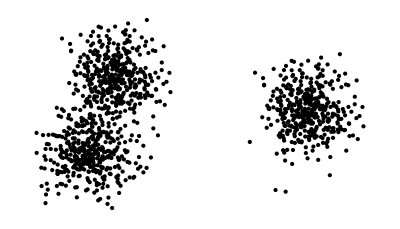

```mathematica
Graphics[Map[Point[#]&,ndOv[2,1]]]
```

```mathematica
(*Export["overlapped2D.tsv",ndOv[2,1]]*)
```

overlapped2D.tsv

## 2D, unbalanced

```mathematica
ndUb[3]=Join[Map[#+{1,6}&,nd[2][400]],Map[#*0.5&,nd2[2][400]],Map[#+{10,2}&,nd2[2][400]]];
```

```mathematica
Dimensions[ndUb[3]]
```

{1200,2}

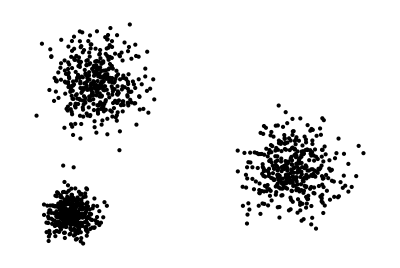

```mathematica
Graphics[Map[Point[#]&,ndUb[3]]]
```

```mathematica
(*Export["unbalanced2D.tsv",ndUb[3]]*)
```

unbalanced2D.tsv

```mathematica
(*Export["unbalanced2D_x10.tsv",ndUb[3]*10]*)
```

unbalanced2D_x10.tsv

```mathematica
(*Export["unbalanced2D_x10E-1.tsv",ndUb[3]/10]*)
```

unbalanced2D_x10E-1.tsv

## 2D, subcluster

```mathematica
ndSubs[5]=Join[Map[#+{0,0}&,nd[2][400]],Map[#*1.1+{0,6}&,nd2[2][400]],Map[#*1.2+{18,0}&,nd2[2][400]],Map[#+{17,6}&,nd[2][400]],Map[#*1.4+{7,17}&,nd2[2][400]]];
```

```mathematica
Dimensions[ndSubs[5]]
```

{2000,2}

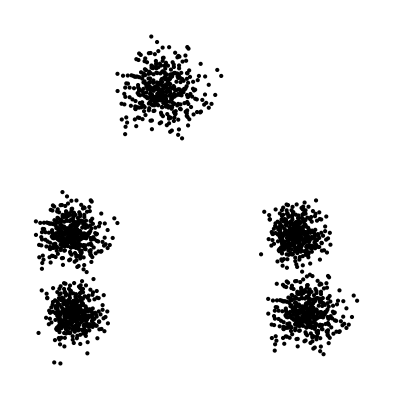

```mathematica
Graphics[Map[Point[#]&,ndSubs[5]]]
```

```mathematica
(*Export["subcluster2D.tsv",ndSubs[5]]*)
```

subcluster2D.tsv

## 2D, noisy

```mathematica
shifts={{6.8,2.5},{4.5,6.1},{4.0,3.2},{2.0,1.7},{8.5,4.8},{2.0,5.4},{5.9,0.3}}
```

{{6.8,2.5},{4.5,6.1},{4.,3.2},{2.,1.7},{8.5,4.8},{2.,5.4},{5.9,0.3}}

```mathematica
scales={0.25,0.3,0.18,0.3,0.28,0.3,0.3}
```

{0.25,0.3,0.18,0.3,0.28,0.3,0.3}

```mathematica
(nd[7,"correct"]=Table[Map[#*scales[[n]]+shifts[[n]]&,nd[2][200]],{n,Length[shifts]}])//Length
```

7

```mathematica
nd[7,"correct","centroids"]=Map[Mean[#]&,nd[7,"correct"]]
```

{{6.78756,2.46707},{4.48507,6.06048},{3.99104,3.17629},{1.98507,1.66048},{8.48607,4.76312},{1.98507,5.36048},{5.88507,0.260483}}

```mathematica
nd[7,"correct","1/10","centroids"]=Map[Mean[#]&,nd[7,"correct"]/10]
```

{{0.678756,0.246707},{0.448507,0.606048},{0.399104,0.317629},{0.198507,0.166048},{0.848607,0.476312},{0.198507,0.536048},{0.588507,0.0260483}}

```mathematica
(nd[7]=Flatten[Table[Map[#*scales[[n]]+shifts[[n]]&,nd[2][200]],{n,Length[shifts]}],1])//Dimensions
```

{1400,2}

```mathematica
(nd[7,"correct","R"]=createClusterdFileR[nd[7,"correct"]])//Length
```

1400

```mathematica
(nd[7,"correct","R","1/10"]=createClusterdFileR[nd[7,"correct"]/10])//Length
```

1400

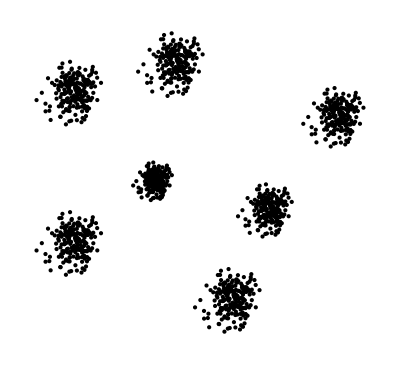

```mathematica
Graphics[Map[Point[#]&,nd[7]],PlotRange->All]
```

```mathematica
(*Export["nd7.tsv",nd[7]]*)
```

```mathematica
(*Export["nd7_x10E-1.tsv",nd[7]/10]*)
```

```mathematica
nd[7,"correct","R"]//Length
```

1400

```mathematica
(*Export["nd7_correct_R.tsv",nd[7,"correct","R"]]*)
```

```mathematica
(*Export["nd7_correct_R.cent.tsv",nd[7,"correct","centroids"]]*)
```

```mathematica
(*Export["nd7_correct_R_x10E-1.tsv",nd[7,"correct","R","1/10"]]*)
```

```mathematica
(*Export["nd7_correct_R_x10E-1.cent.tsv",nd[7,"correct","1/10","centroids"]]*)
```

```mathematica
FindClusters[nd[7],Method->"Agglomerate"]//Length
```

1

```mathematica
nois=Map[#+{5,3.2}&,bg[2][400]*5.4];
```

```mathematica
noisy[7]=Join[nd[7],nois];
```

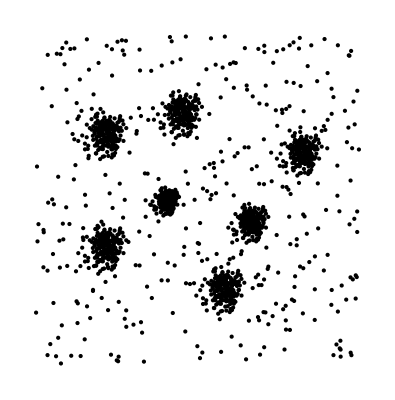

```mathematica
Graphics[Map[Point[#]&,noisy[7]]]
```

```mathematica
(*Export["noisy7.tsv",noisy[7]]*)
```

noisy7.tsv

```mathematica
(*Export["noisy7_x10E-1.tsv",noisy[7]/10]*)
```

noisy7_x10E-1.tsv

```mathematica
FindClusters[noisy[7],7,Method->"Optimize"]//Length
```

7

```mathematica
FindClusters[noisy[7],Method->"Agglomerate"]//Length
```

1

```mathematica
FindClusters[noisy[7],Method->"Optimize"]//Length
```

2

## 2D, 60 samples, 6 clusters, each cluster has 10 samples.

わかりやすいデータ、6クラスタ、60サンプル、各クラスタに10メンバー、2次元

```mathematica
rt6=Map[polarToxy[{1,#}]&,Table[2 Pi n/6,{n,1,6}]]
```

{{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0}}

```mathematica
Graphics[Map[Point[#]&,rt6]]
```

-Graphics-

```mathematica
dataCLrt6=Transpose[Table[rt6,{10}]]
```

{{{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2}},{{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2}},{{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0}},{{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2}},{{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2}},{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}}}

```mathematica
dataFLrt6=Flatten[dataCLrt6,1]
```

{{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}}

```mathematica
(*Export["dataFLrt6.tsv",dataFLrt6]*)
```

dataFLrt6.tsv

## 2D, 50 samples, 10 clusters

```mathematica
rt10=Map[polarToxy[{1,#}]&,Table[2 Pi n/10,{n,1,10}]]//N
```

{{0.809017,0.587785},{0.309017,0.951057},{-0.309017,0.951057},{-0.809017,0.587785},{-1.,0.},{-0.809017,-0.587785},{-0.309017,-0.951057},{0.309017,-0.951057},{0.809017,-0.587785},{1.,0.}}

```mathematica
rt10table5=Transpose[Table[rt10,{5}]];
```

```mathematica
rt10table5R=makeRClusterFromMMAClData[rt10table5]
```

{{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10}}

```mathematica
(*Export["rt10table5R.tsv",rt10table5R]*)
```

rt10table5R.tsv

```mathematica
Directory[]
```

/Users/amanokou/TEST_COLLECTION/ClusteringAdequation/data

## 2D, 100 samples, 10 clusters

```mathematica
rt10=Map[polarToxy[{1,#}]&,Table[2 Pi n/10,{n,1,10}]]//N
```

{{0.809017,0.587785},{0.309017,0.951057},{-0.309017,0.951057},{-0.809017,0.587785},{-1.,0.},{-0.809017,-0.587785},{-0.309017,-0.951057},{0.309017,-0.951057},{0.809017,-0.587785},{1.,0.}}

```mathematica
rt10table10=Transpose[Table[rt10,{10}]];
```

```mathematica
rt10table10R=makeRClusterFromMMAClData[rt10table10]
```

{{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10}}

```mathematica
(*Export["rt10table10R.tsv",rt10table10R]*)
```

rt10table10R.tsv

```mathematica
Directory[]
```

/Users/amanokou/TEST_COLLECTION/ClusteringAdequation/data

## 10D, 100 samples, 10 clusters

```mathematica
id10=IdentityMatrix[10];
```

```mathematica
id10Table10=Transpose[Table[id10,{10}]];
```

```mathematica
id10Table10R=makeRClusterFromMMAClData[id10Table10]
```

{{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10}}

## 10D, 50 samples, 10 clusters

```mathematica
id10=IdentityMatrix[10];
```

```mathematica
id10Table5=Transpose[Table[id10,{5}]];
```

```mathematica
id10Table5R=makeRClusterFromMMAClData[id10Table5]
```

{{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10}}

## TEST

```mathematica
Exp[Exp[7.849258]]
```

2.86921821913×10^1113

```mathematica
Exp[7.849258]
```

2563.83

```mathematica
iris[5]={{5.1 ,3.5 ,1.4 ,0.2 },
{4.9 ,3.0 ,1.4 ,0.2 },
{4.7 ,3.2 ,1.3 ,0.2 },
{4.6 ,3.1 ,1.5 ,0.2},
{5.0 ,3.6 ,1.4,0.2}}
```

{{5.1,3.5,1.4,0.2},{4.9,3.,1.4,0.2},{4.7,3.2,1.3,0.2},{4.6,3.1,1.5,0.2},{5.,3.6,1.4,0.2}}

WCDの検算

```mathematica
iris[5,"clusterd2"]={iris[5][[{1,5}]],iris[5][[{2,3,4}]]}
```

{{{5.1,3.5,1.4,0.2},{5.,3.6,1.4,0.2}},{{4.9,3.,1.4,0.2},{4.7,3.2,1.3,0.2},{4.6,3.1,1.5,0.2}}}

```mathematica
iris[5,"clusterd2","centroid"]=Map[Mean[#]&,iris[5,"clusterd2"]]
```

{{5.05,3.55,1.4,0.2},{4.73333,3.1,1.4,0.2}}

```mathematica
iris[5,"clusterd2","centroid"][[1]]-iris[5,"clusterd2"][[1]]
```

Thread::tdlen: {5.05, 3.55, 1.4, 0.2} + {{-5.1, -3.5, -1.4, -0.2}, {-5., -3.6, -1.4, -0.2}}の長さが異なるオブジェクトは結合することができません．

{{-5.1,-3.5,-1.4,-0.2},{-5.,-3.6,-1.4,-0.2}}+{5.05,3.55,1.4,0.2}

```mathematica
Table[Map[#-iris[5,"clusterd2","centroid"][[n]]&,iris[5,"clusterd2"][[n]]],{n,2}]//TableForm
```

0.05
-0.05
0.
0. | -0.05
0.05
0.
0. | 
0.166667
-0.1
-2.22045×10^-16
-2.77556×10^-17 | -0.0333333
0.1
-0.1
-2.77556×10^-17 | -0.133333
0.
0.1
-2.77556×10^-17

```mathematica
Table[Map[EuclideanDistance[#,iris[5,"clusterd2","centroid"][[n]]]^2&,iris[5,"clusterd2"][[n]]],{n,2}]
```

{{0.005,0.005},{0.0377778,0.0211111,0.0277778}}

```mathematica
Map[Mean[#]&,Table[Map[EuclideanDistance[#,iris[5,"clusterd2","centroid"][[n]]]^2&,iris[5,"clusterd2"][[n]]],{n,2}]]
```

{0.005,0.0288889}

```mathematica
Map[Sqrt[Mean[#]]&,Table[Map[EuclideanDistance[#,iris[5,"clusterd2","centroid"][[n]]]^2&,iris[5,"clusterd2"][[n]]],{n,2}]]
```

{0.0707107,0.169967}

WCD:

```mathematica
iris[5,"clusterd2","WCD"]=Map[Sqrt[Mean[#]]&,Table[Map[EuclideanDistance[#,iris[5,"clusterd2","centroid"][[n]]]^2&,iris[5,"clusterd2"][[n]]],{n,2}]]//Mean
```

0.120339

BCDの検算

```mathematica
iris[5]
```

{{5.1,3.5,1.4,0.2},{4.9,3.,1.4,0.2},{4.7,3.2,1.3,0.2},{4.6,3.1,1.5,0.2},{5.,3.6,1.4,0.2}}

```mathematica
iris[5,"clusterd2","centroid"]
```

{{5.05,3.55,1.4,0.2},{4.73333,3.1,1.4,0.2}}

```mathematica
iris[5,"TOT centroid"]=Mean[iris[5]]
```

{4.86,3.28,1.4,0.2}

```mathematica
Map[EuclideanDistance[iris[5,"TOT centroid"],#]^2&,iris[5,"clusterd2","centroid"]]
```

{0.109,0.0484444}

```mathematica
Map[(EuclideanDistance[iris[5,"TOT centroid"],#]^2)&,iris[5,"clusterd2","centroid"]]
```

{0.109,0.0484444}

```mathematica
iris[5,"BCD prod"]=Map[Length[#]&,iris[5,"clusterd2"]]
```

{2,3}

```mathematica
Map[(EuclideanDistance[iris[5,"TOT centroid"],#]^2)&,iris[5,"clusterd2","centroid"]] iris[5,"BCD prod"]
```

{0.218,0.145333}

BCD

```mathematica
iris[5,"clusterd2","BCD"]=Tr[Map[(EuclideanDistance[iris[5,"TOT centroid"],#]^2)&,iris[5,"clusterd2","centroid"]] iris[5,"BCD prod"]]/10
```

0.0363333

```mathematica
iris[5,"clusterd2","BCD"]
```

0.0363333

```mathematica
iris[5,"clusterd2","WCD"]
```

0.120339

```mathematica
iris[5,"clusterd2","BCD"]-iris[5,"clusterd2","WCD"]
```

-0.0840057

```mathematica
E^(E^(iris[5,"clusterd2","BCD"]-iris[5,"clusterd2","WCD"]))
```

2.50785

```mathematica
1-1/E^(E^(iris[5,"clusterd2","BCD"]-iris[5,"clusterd2","WCD"]))
```

0.601252

```mathematica
1-1/Exp[Exp[iris[5,"clusterd2","BCD"]-iris[5,"clusterd2","WCD"]]]
```

0.601252

```mathematica
EuclideanDistance[{-1,-3,1},{3,6,-2}]//N
```

10.2956